```mathematica
CalculateMathieuEnergies[n_,k_,q_] :=
	Module[{data},
data=Table[MathieuCharacteristicA[i,j]//N,{i,-1*k,k,2*k/(n-1)},{j,-1*q,q,2*q/(n-1)}];
Export["Mathieu_values.json",data,"ExpressionJSON"];]
```

```mathematica
CalculateMathieuEnergies[250,5,3.8589003840022436*0.5]
```

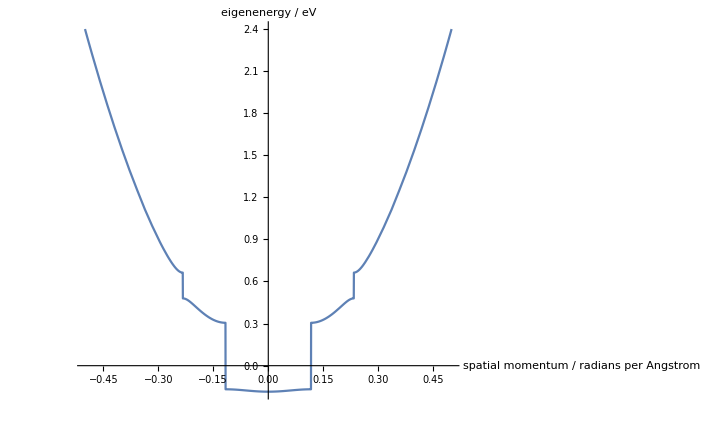

```mathematica
Plot[MathieuCharacteristicA[r/0.037126125988993584/π,3.8589003840022436*0.5]*π^2*(10^10/26.93521)^2*(6.626*10^-34)^2/2/2/π/π/2/(9.11*10^-31)/0.4/(1.60022*10^-19),{r,-.5,.5}, Axes-> True, AxesLabel->{"spatial momentum / radians per Angstrom","eigenenergy / eV"}]
```

```mathematica
CalculateMathieuFunctions[n_,emax_,q_,r_,k_] :=
	Module[{emin,data},
emin=MathieuCharacteristicA[0,q]//N;
data=Table[MathieuC[e,q,x*k*π]//N,{e,emin,emax,(emax-emin)/(n-1)},{x,-r/k,r/k,2*r/k/(n-1)}];
Export["Mathieu_functions.json",data,"ExpressionJSON"];]
```

```mathematica
CalculateMathieuFunctions[250,0.015*132.5520520861412*2,0.01*132.5520520861412,2,0.006334585321891637]
```

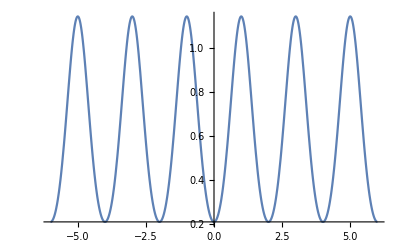

```mathematica
Plot[MathieuC[-1.4281740979293864,3.8589003840022436*0.5,z*π/2],{z,-6,6}]
```

```mathematica
MathieuCharacteristicA[0,3.8589003840022436*0.5]*π^2*(10^10/26.93521)^2*(6.626*10^-34)^2/2/2/π/π/2/(9.11*10^-31)/0.4/(1.60022*10^-19)
```

-0.185266